# Polyhedral Graph

### Author

Eric W. Weisstein
October 12, 2022

This notebook downloaded from http://mathworld.wolfram.com/notebooks/GraphTheory/PolyhedralGraph.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/PolyhedralGraph.html.

©2022 Wolfram Research, Inc. except for portions noted otherwise

## Enumeration by VertexCount

A000944

0, 0, 0, 1, 2, 7, 34, 257, 2606, 32300, 440564, 6384634, 96262938, 1496225352, 23833988129, 387591510244, 6415851530241, 107854282197058

### PolyhedralGraphs

```mathematica
Length/@PolyhedralGraphs/@Range[9]//Timing
```

{1.61 Second,{0,0,0,1,2,7,34,257,2606}}

### PolyhedralGraphQ

```mathematica
Count[#,_?PolyhedralGraphQ]&/@Graphs/@Range[8]//Timing
```

{9.04916,{0,0,0,1,2,7,34,257}}

```mathematica
Count[#,_?PolyhedralGraphQ]&/@PlanarConnectedGraphs/@Range[8]//Timing
```

{3.10808,{0,0,0,1,2,7,34,257}}

### GraphData

```mathematica
Length/@Table[GraphData["Polyhedral",n],{n,9}]
```

{0,0,0,1,2,7,34,257,85}

### plantri

```mathematica
Length/@Table[PolyhedralGraphs[n],{n,10}]//Timing
```

{9.54331,{0,0,0,1,2,7,34,257,2606,32300}}

```mathematica
Do[Print[{n,Length@PolyhedralGraphs[n]//Timing}],{n,11}]
```

{1,{0.000011,0}}

{2,{4.×10^-6,0}}

{3,{3.×10^-6,0}}

{4,{0.006183,1}}

{5,{0.006138,2}}

{6,{0.007137,7}}

{7,{0.013955,34}}

{8,{0.356827,257}}

{9,{1.49726,2606}}

{10,{7.46607,32300}}

{11,{101.438,440564}}

~/src/plantri52/plantri -p -s 13 Polyhedral_13.s6
96262938 polytopes written to Polyhedral_13.s6; cpu=199.83 sec

mkdir 13
cd 13
split -l 10000000 -a 3 --numeric-suffixes=1 ../Polyhedral_13.s6 p

$ ls -lh
total 2.4G
-rw-r--r-- 1 eww users 252M May  4 08:36 p001
-rw-r--r-- 1 eww users 252M May  4 08:36 p002
-rw-r--r-- 1 eww users 248M May  4 08:36 p003
-rw-r--r-- 1 eww users 251M May  4 08:36 p004
-rw-r--r-- 1 eww users 254M May  4 08:36 p005
-rw-r--r-- 1 eww users 255M May  4 08:36 p006
-rw-r--r-- 1 eww users 250M May  4 08:36 p007
-rw-r--r-- 1 eww users 252M May  4 08:36 p008
-rw-r--r-- 1 eww users 253M May  4 08:36 p009
-rw-r--r-- 1 eww users 160M May  4 08:36 p010

### Write to File

```mathematica
Put[Select[PlanarConnectedGraphs[9],KConnectedQ[3,#]&],"PolyhedralGraphs9.m"]//Timing
```

{22910.1 Second,Null}

## Enumeration by EdgeCount

```mathematica
{0,0,0,0,0,1,0,1,2,2,4,12,22,58,158,448,1342,4199,13384,43708,144810,485704}
```

## Graphics

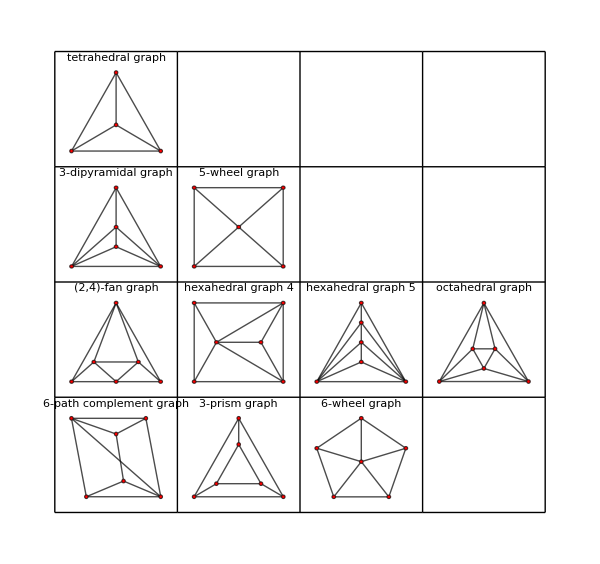

```mathematica
GraphicsGrid[Flatten[Partition[#,UpTo[4]]&/@Map[Show[StyleGraphs[GraphData[#],VertexSize->{"Scaled",.03}],PlotLabel->TextCell[GraphData[#,"Name"],TextAlignment->Center,PageWidth->140],LabelStyle->Directive[12,Black,Italic,FontFamily->"Times"]]&,GraphData["Polyhedral",#]&/@Range[4,6],{2}],1],ImageSize->600,Dividers->{{Thick,{True},Thick},{{Thick},True,Thick}}]
```